### set up

```mathematica
uE[theta_,phi_,Ex_,Ey_,Ez_]:=-mu (Ex Sin[theta]Cos[phi]+Ey Sin[theta]Sin[phi]+Ez Cos[theta])
uDD[t1_,t2_,p1_,p2_]:=mu^2/r^3(Sin[t1]Sin[t2]Cos[p1-p2]-2Cos[t1]Cos[t2])

p[t1_,t2_,p1_,p2_,Ex_,Ey_,Ez_]:=Exp[-beta (uE[t1,p1,Ex,Ey,Ez]+uE[t2,p2,Ex,Ey,Ez])+uDD[t1,t2,p1,p2]]

Fx[t1_,t2_,p1_,p2_,Ex_]:= p[t1,t2,p1,p2,Ex,0,0]Sin[t1]Sin[t2](beta mu(Sin[t1]Cos[p1]+Sin[t2]Cos[p2])+Qx)
Fy[t1_,t2_,p1_,p2_,Ey_]:= p[t1,t2,p1,p2,0,Ey,0]Sin[t1]Sin[t2](beta mu(Sin[t1]Sin[p1]+Sin[t2]Sin[p2])+Qy)
Fz[t1_,t2_,p1_,p2_,Ez_]:= p[t1,t2,p1,p2,0,0,Ez]Sin[t1]Sin[t2](beta mu(Cos[t1]+Cos[t2])+Qz)
```

```mathematica
fxSer=Series[Fx[t1,t2,p1,p2,Ex],{r,Infinity,3},{Ex,0,1}]//Normal;
fySer=Series[Fy[t1,t2,p1,p2,Ey],{r,Infinity,3},{Ey,0,1}]//Normal;
fzSer=Series[Fz[t1,t2,p1,p2,Ez],{r,Infinity,3},{Ez,0,1}]//Normal;
```

```mathematica
h0x=Integrate[fxSer,{t2,0,Pi}]/Pi//Simplify;
h0y=Integrate[fySer,{t2,0,Pi}]/Pi//Simplify;
h0z=Integrate[fzSer,{t2,0,Pi}]/Pi//Simplify;
```

```mathematica
hnx=Integrate[fxSer Cos[n t2],{t2,0,Pi}]2/Pi;
```

```mathematica
hny=Integrate[fySer Cos[n t2],{t2,0,Pi}]2/Pi//Simplify;
```

```mathematica
hnz=Integrate[fzSer Cos[n t2],{t2,0,Pi},Assumptions->n∈Integers&&n>0]2/Pi;
```

```mathematica
dA0dt1x=Integrate[h0x,{t1,0,T}]/.{T->t1};
```

```mathematica
dA0dt1y=Integrate[h0y,{t1,0,T}]/.{T->t1};
```

$Aborted

```mathematica
dA0dt1z=Integrate[h0z,{t1,0,T}]/.{T->t1}
```

-(5 beta^2 Ez mu^2 (-1+Cos[t1]))/(3 π)-(2 Qz (-1+Cos[t1]))/π+(4 beta^2 Ez mu^4 (-1+Cos[t1]))/(3 π r^3)+(beta^2 Ez mu^2 (-2+3 Cos[t1]-Cos[3 t1]))/(6 π)-(2 beta^2 Ez mu^4 (-2+3 Cos[t1]-Cos[3 t1]))/(9 π r^3)-(beta mu^3 (Sin[p1-p2-2 t1]+2 Sin[p1-p2-t1]) Sin[t1/2]^2)/(12 r^3)-(beta Ez mu^3 Qz (Sin[p1-p2-2 t1]+2 Sin[p1-p2-t1]) Sin[t1/2]^2)/(12 r^3)+(beta mu Sin[t1]^2)/π+(beta Ez mu Qz Sin[t1]^2)/π-(2 beta mu^3 Sin[t1]^2)/(3 π r^3)-(2 beta Ez mu^3 Qz Sin[t1]^2)/(3 π r^3)-(beta^2 Ez mu^4 Sin[p1-p2-2 t1] Sin[t1]^2)/(32 r^3)+(beta^2 Ez mu^4 (t1 Cos[p1-p2]-Cos[p1-p2-t1] Sin[t1]))/(16 r^3)+(mu^2 Qz (t1 Cos[p1-p2]-Cos[p1-p2-t1] Sin[t1]))/(8 r^3)+(beta^2 Ez mu^4 (t1 Cos[p1-p2]-Cos[p1-p2+t1] Sin[t1]))/(16 r^3)+(mu^2 Qz (t1 Cos[p1-p2]-Cos[p1-p2+t1] Sin[t1]))/(8 r^3)+(beta^2 Ez mu^4 Sin[t1]^2 Sin[p1-p2+2 t1])/(32 r^3)+(beta mu^3 Sin[t1/2]^2 (2 Sin[p1-p2+t1]+Sin[p1-p2+2 t1]))/(12 r^3)+(beta Ez mu^3 Qz Sin[t1/2]^2 (2 Sin[p1-p2+t1]+Sin[p1-p2+2 t1]))/(12 r^3)

```mathematica
dAndt1x = Integrate[(hnx/.{t1->xi}) Cosh[n(t1-xi)],{xi,0,t1}];
```

```mathematica
dAndt1y = Integrate[(hny/.{t1->xi}) Cosh[n(t1-xi)],{xi,0,t1}]
```

(Sin[t1] (1152 beta mu n r^3+1536 beta^2 Ez mu^2 n r^3-1352 beta mu n^3 r^3-992 beta^2 Ez mu^2 n^3 r^3+208 beta mu n^5 r^3+184 beta^2 Ez mu^2 n^5 r^3-8 beta mu n^7 r^3-8 beta^2 Ez mu^2 n^7 r^3+4608 n Qz r^3+1152 beta Ez mu n Qz r^3-1952 n^3 Qz r^3-1352 beta Ez mu n^3 Qz r^3+232 n^5 Qz r^3+208 beta Ez mu n^5 Qz r^3-8 n^7 Qz r^3-8 beta Ez mu n^7 Qz r^3+16 beta^2 Ez mu^4 n (-144+169 n^2-26 n^4+n^6) Cos[t1]^3-8 n Cos[n π] ((-16+n^2) (beta^2 Ez mu^2 (12-7 n^2+n^4)+(36-13 n^2+n^4) Qz-beta mu (9-10 n^2+n^4) (1+Ez Qz)) r^3+mu (2 mu (-144+169 n^2-26 n^4+n^6) Qz+2 beta^2 Ez mu (9-10 n^2+n^4) (mu^2 (-10+n^2)-(-16+n^2) r^3)-beta (64-20 n^2+n^4) (1+Ez Qz) (2 mu^2 (-3+n^2)-(-9+n^2) r^3)) Cos[t1]-beta mu^2 (-16+n^2) (4 beta Ez mu^2 (12-7 n^2+n^4)-2 mu (9-10 n^2+n^4) (1+Ez Qz)-beta Ez (36-13 n^2+n^4) r^3) Cos[t1]^2+2 beta^2 Ez mu^4 (-144+169 n^2-26 n^4+n^6) Cos[t1]^3)+576 beta^2 Ez mu^4 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+1024 beta mu^3 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[t1]-784 beta^2 Ez mu^4 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[t1]-320 beta mu^3 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+224 beta^2 Ez mu^4 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+16 beta mu^3 n^6 Cos[p1] Cos[p2] Sin[n π] Sin[t1]-16 beta^2 Ez mu^4 n^6 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+2304 mu^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]-2704 mu^2 n^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+1024 beta Ez mu^3 n^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+416 mu^2 n^4 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]-320 beta Ez mu^3 n^4 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]-16 mu^2 n^6 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+16 beta Ez mu^3 n^6 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+576 beta^2 Ez mu^4 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+1024 beta mu^3 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[t1]-784 beta^2 Ez mu^4 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[t1]-320 beta mu^3 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+224 beta^2 Ez mu^4 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+16 beta mu^3 n^6 Sin[p1] Sin[p2] Sin[n π] Sin[t1]-16 beta^2 Ez mu^4 n^6 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+2304 mu^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]-2704 mu^2 n^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+1024 beta Ez mu^3 n^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+416 mu^2 n^4 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]-320 beta Ez mu^3 n^4 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]-16 mu^2 n^6 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+16 beta Ez mu^3 n^6 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+2 mu n Cos[t1] (4 (2 mu (-144+169 n^2-26 n^4+n^6) Qz+2 beta^2 Ez mu (9-10 n^2+n^4) (mu^2 (-10+n^2)-(-16+n^2) r^3)+beta (64-20 n^2+n^4) (1+Ez Qz) (2 mu^2 (-3+n^2)-(-9+n^2) r^3))-21 beta^2 Ez mu^3 n^2 (12+n^3) Sin[p1] Sin[p2] Sin[n π] Sin[t1])+8 beta mu^2 (-16+n^2) Cos[t1]^2 (n (4 beta Ez mu^2 (12-7 n^2+n^4)+2 mu (9-10 n^2+n^4) (1+Ez Qz)-beta Ez (36-13 n^2+n^4) r^3)-2 beta Ez mu^2 (9-10 n^2+n^4) Cos[p1] Cos[p2] Sin[n π] Sin[t1]-2 beta Ez mu^2 (9-10 n^2+n^4) Sin[p1] Sin[p2] Sin[n π] Sin[t1])+1152 beta mu^3 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-1352 beta mu^3 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+1024 beta^2 Ez mu^4 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+208 beta mu^3 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-320 beta^2 Ez mu^4 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-8 beta mu^3 n^6 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+16 beta^2 Ez mu^4 n^6 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+1152 beta Ez mu^3 Qz Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-1352 beta Ez mu^3 n^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+208 beta Ez mu^3 n^4 Qz Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-8 beta Ez mu^3 n^6 Qz Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+1152 beta mu^3 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-1352 beta mu^3 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+1024 beta^2 Ez mu^4 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+252 beta^2 Ez mu^4 n^3 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+208 beta mu^3 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-320 beta^2 Ez mu^4 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-8 beta mu^3 n^6 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+37 beta^2 Ez mu^4 n^6 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+1152 beta Ez mu^3 Qz Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-1352 beta Ez mu^3 n^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+208 beta Ez mu^3 n^4 Qz Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-8 beta Ez mu^3 n^6 Qz Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]) Sinh[n t1])/(4 (-4+n) (-3+n) (-2+n) (-1+n) n^2 (1+n) (2+n) (3+n) (4+n) π r^3)

```mathematica
dAndt1z = Integrate[(hnz/.{t1->xi}) Cosh[n(t1-xi)],{xi,0,t1}]
```

(2 ((72 beta mu^3 n Cos[t1])/(1+n^2)+786+(beta Ez 5 Sin[n π] Sinh[n t1])/(2 (9+n^2))))/((-4+n) (-3+n) (-2+n) (-1+n) n (1+n) (2+n) (3+n) (4+n) π r^3)
 |  |  |  |

```mathematica
Integrate[hn Cosh[n(Pi-xi)],{xi,0,Pi}]
```

(Sin[t1] (1152 beta mu n r^3+1536 beta^2 Ez mu^2 n r^3-1352 beta mu n^3 r^3-992 beta^2 Ez mu^2 n^3 r^3+208 beta mu n^5 r^3+184 beta^2 Ez mu^2 n^5 r^3-8 beta mu n^7 r^3-8 beta^2 Ez mu^2 n^7 r^3+4608 n Qz r^3+1152 beta Ez mu n Qz r^3-1952 n^3 Qz r^3-1352 beta Ez mu n^3 Qz r^3+232 n^5 Qz r^3+208 beta Ez mu n^5 Qz r^3-8 n^7 Qz r^3-8 beta Ez mu n^7 Qz r^3+16 beta^2 Ez mu^4 n (-144+169 n^2-26 n^4+n^6) Cos[t1]^3-8 n Cos[n π] ((-16+n^2) (beta^2 Ez mu^2 (12-7 n^2+n^4)+(36-13 n^2+n^4) Qz-beta mu (9-10 n^2+n^4) (1+Ez Qz)) r^3+mu (2 mu (-144+169 n^2-26 n^4+n^6) Qz+2 beta^2 Ez mu (9-10 n^2+n^4) (mu^2 (-10+n^2)-(-16+n^2) r^3)-beta (64-20 n^2+n^4) (1+Ez Qz) (2 mu^2 (-3+n^2)-(-9+n^2) r^3)) Cos[t1]-beta mu^2 (-16+n^2) (4 beta Ez mu^2 (12-7 n^2+n^4)-2 mu (9-10 n^2+n^4) (1+Ez Qz)-beta Ez (36-13 n^2+n^4) r^3) Cos[t1]^2+2 beta^2 Ez mu^4 (-144+169 n^2-26 n^4+n^6) Cos[t1]^3)+576 beta^2 Ez mu^4 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+1024 beta mu^3 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[t1]-784 beta^2 Ez mu^4 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[t1]-320 beta mu^3 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+224 beta^2 Ez mu^4 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+16 beta mu^3 n^6 Cos[p1] Cos[p2] Sin[n π] Sin[t1]-16 beta^2 Ez mu^4 n^6 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+2304 mu^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]-2704 mu^2 n^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+1024 beta Ez mu^3 n^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+416 mu^2 n^4 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]-320 beta Ez mu^3 n^4 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]-16 mu^2 n^6 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+16 beta Ez mu^3 n^6 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+576 beta^2 Ez mu^4 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+1024 beta mu^3 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[t1]-784 beta^2 Ez mu^4 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[t1]-320 beta mu^3 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+224 beta^2 Ez mu^4 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+16 beta mu^3 n^6 Sin[p1] Sin[p2] Sin[n π] Sin[t1]-16 beta^2 Ez mu^4 n^6 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+2304 mu^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]-2704 mu^2 n^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+1024 beta Ez mu^3 n^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+416 mu^2 n^4 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]-320 beta Ez mu^3 n^4 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]-16 mu^2 n^6 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+16 beta Ez mu^3 n^6 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+2 mu n Cos[t1] (4 (2 mu (-144+169 n^2-26 n^4+n^6) Qz+2 beta^2 Ez mu (9-10 n^2+n^4) (mu^2 (-10+n^2)-(-16+n^2) r^3)+beta (64-20 n^2+n^4) (1+Ez Qz) (2 mu^2 (-3+n^2)-(-9+n^2) r^3))-21 beta^2 Ez mu^3 n^2 (12+n^3) Sin[p1] Sin[p2] Sin[n π] Sin[t1])+8 beta mu^2 (-16+n^2) Cos[t1]^2 (n (4 beta Ez mu^2 (12-7 n^2+n^4)+2 mu (9-10 n^2+n^4) (1+Ez Qz)-beta Ez (36-13 n^2+n^4) r^3)-2 beta Ez mu^2 (9-10 n^2+n^4) Cos[p1] Cos[p2] Sin[n π] Sin[t1]-2 beta Ez mu^2 (9-10 n^2+n^4) Sin[p1] Sin[p2] Sin[n π] Sin[t1])+1152 beta mu^3 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-1352 beta mu^3 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+1024 beta^2 Ez mu^4 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+208 beta mu^3 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-320 beta^2 Ez mu^4 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-8 beta mu^3 n^6 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+16 beta^2 Ez mu^4 n^6 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+1152 beta Ez mu^3 Qz Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-1352 beta Ez mu^3 n^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+208 beta Ez mu^3 n^4 Qz Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-8 beta Ez mu^3 n^6 Qz Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+1152 beta mu^3 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-1352 beta mu^3 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+1024 beta^2 Ez mu^4 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+252 beta^2 Ez mu^4 n^3 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+208 beta mu^3 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-320 beta^2 Ez mu^4 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-8 beta mu^3 n^6 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+37 beta^2 Ez mu^4 n^6 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+1152 beta Ez mu^3 Qz Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-1352 beta Ez mu^3 n^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+208 beta Ez mu^3 n^4 Qz Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-8 beta Ez mu^3 n^6 Qz Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]) Sinh[n π])/(4 (-4+n) (-3+n) (-2+n) (-1+n) n^2 (1+n) (2+n) (3+n) (4+n) π r^3)

```mathematica
%/.{Ez->0}//Simplify
```

-((2 Sin[t1] (9 beta mu n r^3-10 beta mu n^3 r^3+beta mu n^5 r^3+36 n Qz r^3-13 n^3 Qz r^3+n^5 Qz r^3-mu n (2 mu (9-10 n^2+n^4) Qz+beta (-4+n^2) (2 mu^2 (-3+n^2)-(-9+n^2) r^3)) Cos[t1]-2 beta mu^3 n (9-10 n^2+n^4) Cos[t1]^2+n Cos[n π] (-(-9+n^2) (beta mu (-1+n^2)-(-4+n^2) Qz) r^3-mu (-2 mu (9-10 n^2+n^4) Qz+beta (-4+n^2) (2 mu^2 (-3+n^2)-(-9+n^2) r^3)) Cos[t1]+2 beta mu^3 (9-10 n^2+n^4) Cos[t1]^2)+8 beta mu^3 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[t1]-2 beta mu^3 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+18 mu^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]-20 mu^2 n^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+2 mu^2 n^4 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+8 beta mu^3 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[t1]-2 beta mu^3 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+18 mu^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]-20 mu^2 n^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+2 mu^2 n^4 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+9 beta mu^3 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-10 beta mu^3 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+beta mu^3 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+9 beta mu^3 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-10 beta mu^3 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+beta mu^3 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]) Sinh[n π])/((-3+n) (-2+n) (-1+n) n^2 (1+n) (2+n) (3+n) π r^3))

```mathematica
Simplify[%]
```

1/(960 r^3)Sin[t2] (-16 beta mu (114 beta^2 Ez^2 mu^4-120 (1+Ez Qz) r^3+mu^2 (80+80 Ez Qz-105 beta^2 Ez^2 r^3)) Cos[t2]+5 (-256 beta^2 Ez mu^4-128 beta^2 Ez^2 mu^4 Qz+320 beta^2 Ez mu^2 r^3+384 Qz r^3+160 beta^2 Ez^2 mu^2 Qz r^3-32 beta^2 Ez mu^2 (2+Ez Qz) (4 mu^2-3 r^3) Cos[2 t2]-48 beta^3 Ez^2 mu^3 (2 mu^2-r^3) Cos[3 t2]-3 beta^3 Ez^2 mu^5 π Sin[p1-p2-4 t2]-12 beta^2 Ez mu^4 π Sin[p1-p2-3 t2]-6 beta^2 Ez^2 mu^4 π Qz Sin[p1-p2-3 t2]-24 beta mu^3 π Sin[p1-p2-2 t2]-15 beta^3 Ez^2 mu^5 π Sin[p1-p2-2 t2]-24 beta Ez mu^3 π Qz Sin[p1-p2-2 t2]-24 beta^2 Ez mu^4 π Sin[p1-p2-t2]-48 mu^2 π Qz Sin[p1-p2-t2]-12 beta^2 Ez^2 mu^4 π Qz Sin[p1-p2-t2]+24 beta^2 Ez mu^4 π Sin[p1-p2+t2]+48 mu^2 π Qz Sin[p1-p2+t2]+12 beta^2 Ez^2 mu^4 π Qz Sin[p1-p2+t2]+24 beta mu^3 π Sin[p1-p2+2 t2]+15 beta^3 Ez^2 mu^5 π Sin[p1-p2+2 t2]+24 beta Ez mu^3 π Qz Sin[p1-p2+2 t2]+12 beta^2 Ez mu^4 π Sin[p1-p2+3 t2]+6 beta^2 Ez^2 mu^4 π Qz Sin[p1-p2+3 t2]+3 beta^3 Ez^2 mu^5 π Sin[p1-p2+4 t2]))

```mathematica
Integrate[Fz[t1,t2,p1,p2,Ez],{t1,0,Pi}]
```

$Aborted

```mathematica
Integrate[Exp[J Cos[t1-t2]],{t1,0,2Pi},{t2,0,2Pi}]/(2Pi)^2
```

BesselI[0,J]

```mathematica
Integrate[Exp[J Cos[t1-t2]](1+muE(Sin[t1]+Sin[t2])),{t1,0,2Pi},{t2,0,2Pi}]/(2Pi)^2
```

BesselI[0,J]

### 2D Heisenberg model

```mathematica
buE[theta_,Ex_,Ey_]:=-bmu (Ex Cos[theta]+Ey Sin[theta])
buDD[t1_,t2_]:=-bJ Cos[t2-t1]

p[t1_,t2_,Ex_,Ey_]:=Exp[(buE[t1,Ex,Ey]+buE[t2,Ex,Ey])-buDD[t1,t2]]
q[Ex_,Ey_]:=Integrate[p[t1,t2,Ex,Ey],{t1,0,2Pi},{t2,0,2Pi}]
```

```mathematica
Qx0[bJ_]:=Release[0 Integrate[Exp[bJ Cos[t2-t1]],{t1,0,2Pi},{t2,0,2Pi}]]
Qx0[bJ]
```

0

```mathematica
chi0[t1_,t2_]:=bmu(Cos[t1]+Cos[t2-t1]-Cos[t2]-1)+1/2 Qx0[bJ] t1(t2-t1)
```

```mathematica
v10[t1_,t2_]:=Release[D[chi0[t1,t2],t2]+bmu Sin[t1]+1/2 t1 Qx0[bJ]//FullSimplify]
v10[t1,t2]
v20[t1_,t2_]:=Release[-D[chi0[t1,t2],t1]+bmu Sin[t2]+1/2 t2 Qx0[bJ]//FullSimplify]
v20[t1,t2]
v10[t1,t2]-v20[t2,t1]//Simplify
```

bmu (Sin[t1]+Sin[t1-t2]+Sin[t2])

bmu (Sin[t1]+Sin[t1-t2]+Sin[t2])

2 bmu Sin[t1-t2]

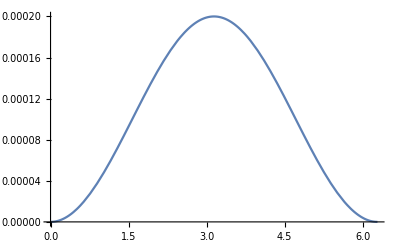

```mathematica
Plot[v10[t1,Pi-.0001]/.{bJ->1,bmu->1},{t1,0,2Pi}]
```

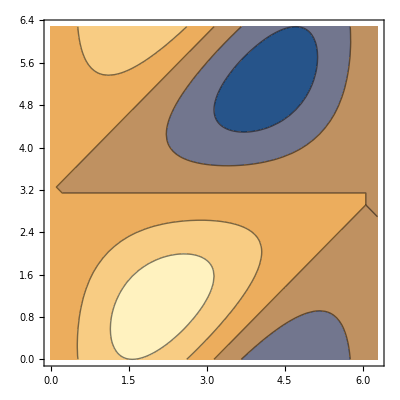

-Graphics-

```mathematica
ContourPlot[v10[t1,t2]/.{bJ->1,bmu->1},{t1,0,2Pi},{t2,0,2Pi}]
ContourPlot[v20[t1,t2]/.{bJ->1,bmu->1},{t1,0,2Pi},{t2,0,2Pi}]
```

### Searching for solution by choosing a general form

```mathematica
TrigExpand[Sin[t2-t1]]
```

-Cos[t2] Sin[t1]+Cos[t1] Sin[t2]

```mathematica
Clear[eqn]
eqn[v_]:=D[v[t1,t2],t1]+D[v[t2,t1],t2]-v[t1,t2](bmuE Sin[t1]-bJ (-Cos[t2] Sin[t1]+Cos[t1] Sin[t2]))-v[t2,t1](bmuE Sin[t2]+bJ (-Cos[t2] Sin[t1]+Cos[t1] Sin[t2]))+bmu(Cos[t1]+Cos[t2])-Qx
eqn0[v_]:=D[v[t1,t2],t1]+D[v[t2,t1],t2]-v[t1,t2](-bJ (-Cos[t2] Sin[t1]+Cos[t1] Sin[t2]))-v[t2,t1](+bJ (-Cos[t2] Sin[t1]+Cos[t1] Sin[t2]))+bmu(Cos[t1]+Cos[t2])-Qx0
eqn1[v0_,v1_]:=D[v1[t1,t2],t1]+D[v1[t2,t1],t2]-v0[t1,t2]bmu Sin[t1]+v1[t1,t2]bJ (-Cos[t2] Sin[t1]+Cos[t1] Sin[t2])-v0[t2,t1] bmu Sin[t2]-v1[t2,t1]bJ (-Cos[t2] Sin[t1]+Cos[t1] Sin[t2])-Qx1
```

```mathematica
(*(∂v1[t1,t2])/(∂t1)+(∂v1[t2,t1])/(∂t2)-(v0[t1,t2]+Ε v1[t1,t2])(b mu Ε Sin[t1]-b j Sin[t2-t1])
-v0[t1,t2] b mu Ε Sin[t1]+Ε v1[t1,t2] b j Sin[t2-t1] 

-(v0[t2,t1]+v1[t2,t1] Ε) (b mu Ε Sin[t2]+ b j Sin[t2-t1])
-v0[t2,t1] b mu Ε Sin[t2] -v1[t2,t1] Ε  b j Sin[t2-t1]*)
```

```mathematica
N1 = N2 = N3 = N4 =3;
M1 = M2 = 1;
Clear[term]
term[n1_,n2_,n3_,n4_,m1_,m2_,t1_,t2_]:=a[n1,n2,n3,n4,m1,m2]Sin[t1]^n1 Cos[t1]^n2 Sin[t2]^n3 Cos[t2]^n4 t1^m1 t2^m2
myv[t1_,t2_]:=Sum[term[n1,n2,n3,n4,m1,m2,t1,t2],{n1,0,N1},{n2,0,N2},{n3,0,N3},{n4,0,N4},{m1,0,M1},{m2,0,M2}]
rename={Sin[t1]->s1,Cos[t1]->c1,Sin[t2]->s2,Cos[t2]->c2};
varList=Flatten[Table[a[n1,n2,n3,n4,m1,m2],{n1,0,N1},{n2,0,N2},{n3,0,N3},{n4,0,N4},{m1,0,M1},{m2,0,M2}]];
```

```mathematica
myeqn0=eqn0[myv]/.rename
Flatten[CoefficientList[myeqn0,{s1,c1,s2,c2,t1,t2}]];
aEqns0=(#==0&/@%);
soln0=Solve[aEqns0,varList];
soln0[[1]]//TableForm;
myv[t1,t2]/.soln0[[1]];
myvSoln[t1_,t2_]:=Release[%]
myvSoln[t1,t2]/.{a[n1_,n2_,n3_,n4_,m1_,m2_]:>0};
myvSoln0[t1_,t2_]:=Release[%]
myvSoln0[t1,t2]
eqn0[myvSoln0]//Simplify
```

```mathematica
myeqn1=eqn1[myvSoln0,myv]/.rename;
Flatten[CoefficientList[myeqn1,{s1,c1,s2,c2,t1,t2}]];
aEqns1=(#==0&/@%);
aEqns1//TableForm
soln1=Solve[aEqns1,varList];
soln1[[1]]//TableForm;
myv[t1,t2]/.soln1[[1]]
myvSoln[t1_,t2_]:=Release[%]
myvSoln[t1,t2]/.{a[n1_,n2_,n3_,n4_,m1_,m2_]:>0};
myvSoln1[t1_,t2_]:=Release[%]
myvSoln1[t1,t2]
eqn1[myvSoln0,myvSoln1]//Simplify
```

1
 |  |  |  |

Solve::svars: Equations may not give solutions for all "solve" variables.

(Qx1 t1)/2+(Qx1 t2)/2+783+(1/3 a[1,2,1,2,0,0]-a[1,3,2,2,1,0]/(3 bJ)+2/3 a[2,1,0,3,0,0]) Sin[t1]^3 Sin[t2]^3
 |  |  |  |

(Qx1 t1)/2+(Qx1 t2)/2-1/2 bmu Qx0 t1 Cos[t1]-1/2 bmu Qx0 t2 Cos[t1]-1/2 bmu^2 t2 Cos[t1]^2-1/2 bmu Qx0 t1 Cos[t2]-1/2 bmu Qx0 t2 Cos[t2]-bmu^2 t2 Cos[t1] Cos[t2]-1/2 bmu^2 t1 Cos[t2]^2+bmu Qx0 Sin[t1]+1/2 bmu^2 Cos[t1] Sin[t1]-1/2 bmu^2 t2 Sin[t1]^2+1/2 bJ bmu^2 t1 Cos[t2]^2 Sin[t1]^2-1/2 bJ bmu^2 t2 Cos[t2]^2 Sin[t1]^2+bmu Qx0 Sin[t2]+1/2 bmu^2 Cos[t2] Sin[t2]-bmu^2 t1 Sin[t1] Sin[t2]-1/2 bmu^2 t1 Sin[t2]^2-1/2 bJ bmu^2 t1 Cos[t1]^2 Sin[t2]^2+1/2 bJ bmu^2 t2 Cos[t1]^2 Sin[t2]^2

0

$OutputSizeLimit::nosess: This output can only be updated in the same kernel session that generated it.

```mathematica
myeqn=eqn[myv]/.rename //Simplify
Flatten[CoefficientList[myeqn,{s1,c1,s2,c2,t1,t2}]]/.bmuE->0;
%==Table[0,{n,Length[%]}];
soln=Solve[%,varList];
soln[[1]]//TableForm;
myv[t1,t2]/.soln[[1]]
myvSoln[t1_,t2_]:=Release[myv[t1,t2]/.soln[[1]]]
myvSolnNoa[t1_,t2_]:=Release[myv[t1,t2]/.soln[[1]]]/.{a[n1_,n2_,n3_,n4_,m1_,m2_]:>0};
myvSolnNoa[t1,t2]
eqn[myvSolnNoa]/.bmuE->0//Simplify
```

bmu (c1+c2)-Qx+5564+(bJ c2 s1-bmuE s2-bJ c1 s2) (a[0,0,0,0,0,0]+t2 a[0,5]+510+t1 (a[0,0,0,0,0,1]+255+t2 (a[0,0,0,0,1,1]+65+c1^3 (1))))
 |  |  |  |

Solve::svars: Equations may not give solutions for all "solve" variables.

(Qx t1)/2+(Qx t2)/2+781+(1/3 a[1,2,1,2,0,0]-a[1,3,2,2,1,0]/(3 bJ)+2/3 a[2,1,0,3,0,0]) Sin[t1]^3 Sin[t2]^3
 |  |  |  |

(Qx t1)/2+(Qx t2)/2-bmu Sin[t1]-bmu Sin[t2]

0

```mathematica
coeffList=Flatten[CoefficientList[myeqn,{s1,c1,s2,c2,t1,t2}]]/.bmuE->0;
(*Select[%,#≠0&]*)
coeffList//TableForm
coeffList==Table[0,{n,Length[%]}];
soln=Solve[%,varList];
soln[[1]]//TableForm
myv[t1,t2]/.soln[[1]]
myvSoln[t1_,t2_]:=Release[myv[t1,t2]/.soln[[1]]]
myvSolnNoa[t1_,t2_]:=Release[myv[t1,t2]/.soln[[1]]]/.{a[n1_,n2_,n3_,n4_,m1_,m2_]:>0};
myvSolnNoa[t1,t2]
eqn[myvSolnNoa]//Simplify
```

1
 |  |  |  |

Solve::svars: Equations may not give solutions for all "solve" variables.

1
 |  |  |  |

(Qx t1)/2+(Qx t2)/2+781+(1/3 a[1,2,1,2,0,0]-a[1,3,2,2,1,0]/(3 bJ)+2/3 a[2,1,0,3,0,0]) Sin[t1]^3 Sin[t2]^3
 |  |  |  |

(Qx t1)/2+(Qx t2)/2-bmu Sin[t1]-bmu Sin[t2]

1/2 bmuE (Sin[t1]+Sin[t2]) (-Qx (t1+t2)+2 bmu Sin[t1]+2 bmu Sin[t2])